```mathematica
FindAlwaysDifferent[g_]:=Block[{sol =Solve[ ToEquations[g],SymbolRange[g]],result={},localsol,count},
count=Length[sol];
Monitor[
Table[
With[
{v1=e[[1]],v2=e[[2]]},
If[VertexDegree[g,v1]>3&&VertexDegree[g,v2]>3,
localsol=Map[{Symbol["x"<>ToString[v1]],Symbol["x"<>ToString[v2]]}/.#&,sol];
localsol=Select[localsol,#[[1]]≠#[[2]]&];
localsol=Length[localsol];
If[localsol==count,
AppendTo[result,v1<->v2]
]
]
]
,{e,EdgeList[GraphComplement[g]]}
],
e];
result
]
```

```mathematica
Select[
Monitor[
Table[
With[
{g=Graph[plantri[[k]]]},
Print[k];
With[
{res={k,VertexCount[g],g,FindAlwaysDifferent[g]}},
Print[res];res]
],
{k,2,2}
],
k],
#[[3]]≠{}&
]//TableForm
```

2

$Aborted

```mathematica
FindAlwaysDifferent[Graph[plantri[[2]]]]
```

{}

```mathematica
2<->10,2<->18,4<->7,4<->17,7<->17,10<->18
```

```mathematica
FindAlwaysSame[g_]:=Block[{sol =Solve[ ToEquations[g],SymbolRange[g]],result={},localsol,count,edges=EdgeList[GraphComplement[g]]},
Print["solved"];
Print[Length[sol]];
count=Length[sol];
Monitor[
Table[
With[
{v1=e[[1]],v2=e[[2]]},
localsol=Map[{Symbol["x"<>ToString[v1]],Symbol["x"<>ToString[v2]]}/.#&,sol];
localsol=Select[localsol,#[[1]]==#[[2]]&];
localsol=Length[localsol];
If[localsol==count,
AppendTo[result,v1<->v2]
]
]
,{e,edges}
],
{e,edges}];
result
]
```

```mathematica
FindAlwaysSame[Graph[plantri[[2]]]]
```

solved

480

{}

```mathematica
ToEquations[Graph[plantri[[11]]]]
```

x1∈Integers&&x2∈Integers&&x3∈Integers&&x4∈Integers&&x5∈Integers&&x6∈Integers&&x7∈Integers&&x8∈Integers&&x9∈Integers&&x10∈Integers&&x11∈Integers&&x12∈Integers&&x13∈Integers&&x14∈Integers&&x15∈Integers&&x16∈Integers&&x17∈Integers&&x18∈Integers&&1≤x1≤4&&1≤x2≤4&&1≤x3≤4&&1≤x4≤4&&1≤x5≤4&&1≤x6≤4&&1≤x7≤4&&1≤x8≤4&&1≤x9≤4&&1≤x10≤4&&1≤x11≤4&&1≤x12≤4&&1≤x13≤4&&1≤x14≤4&&1≤x15≤4&&1≤x16≤4&&1≤x17≤4&&1≤x18≤4&&x1≠x2&&x1≠x3&&x1≠x4&&x1≠x5&&x1≠x6&&x2≠x6&&x2≠x7&&x2≠x8&&x2≠x3&&x3≠x8&&x3≠x9&&x3≠x4&&x4≠x9&&x4≠x10&&x4≠x5&&x5≠x10&&x5≠x11&&x5≠x12&&x5≠x6&&x6≠x12&&x6≠x13&&x6≠x7&&x7≠x13&&x7≠x14&&x7≠x8&&x8≠x14&&x8≠x15&&x8≠x9&&x9≠x15&&x9≠x16&&x9≠x10&&x10≠x16&&x10≠x11&&x11≠x16&&x11≠x17&&x11≠x12&&x12≠x17&&x12≠x18&&x12≠x13&&x13≠x18&&x13≠x14&&x14≠x18&&x14≠x15&&x15≠x18&&x15≠x17&&x15≠x16&&x16≠x17&&x17≠x18

```mathematica
FindAlwaysSame[Graph[plantri[[11]]]]
```

solved

{{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→1,x8→4,x9→1,x10→4,x11→1,x12→2,x13→3,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→3,x8→1,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→3,x8→1,x9→4,x10→1,x11→4,x12→2,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→3,x8→1,x9→4,x10→1,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→1,x2→2,x3→3,x4→2,x5→3,x6→4,x7→3,x8→4,x9→1,x10→4,x11→2,x12→1,x13→2,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→2,x3→3,x4→2,x5→4,x6→3,x7→1,x8→4,x9→1,x10→3,x11→1,x12→2,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→1,x2→2,x3→3,x4→2,x5→4,x6→3,x7→1,x8→4,x9→1,x10→3,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→1,x2→2,x3→3,x4→2,x5→4,x6→3,x7→1,x8→4,x9→1,x10→3,x11→2,x12→1,x13→2,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→2,x3→3,x4→2,x5→4,x6→3,x7→4,x8→1,x9→4,x10→1,x11→3,x12→2,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→1,x2→2,x3→3,x4→2,x5→4,x6→3,x7→4,x8→1,x9→4,x10→3,x11→2,x12→1,x13→2,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→3,x7→1,x8→4,x9→1,x10→3,x11→1,x12→4,x13→2,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→3,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→3,x11→1,x12→3,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→3,x11→4,x12→1,x13→3,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→1,x12→3,x13→1,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→1,x11→4,x12→3,x13→1,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→1,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→2,x12→1,x13→2,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→3,x4→4,x5→3,x6→4,x7→3,x8→1,x9→2,x10→1,x11→4,x12→2,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→1,x2→2,x3→4,x4→2,x5→3,x6→4,x7→1,x8→3,x9→1,x10→4,x11→1,x12→2,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→1,x2→2,x3→4,x4→2,x5→3,x6→4,x7→1,x8→3,x9→1,x10→4,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→1,x2→2,x3→4,x4→2,x5→3,x6→4,x7→1,x8→3,x9→1,x10→4,x11→2,x12→1,x13→2,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→2,x3→4,x4→2,x5→3,x6→4,x7→3,x8→1,x9→3,x10→1,x11→4,x12→2,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→1,x2→2,x3→4,x4→2,x5→3,x6→4,x7→3,x8→1,x9→3,x10→4,x11→2,x12→1,x13→2,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→1,x2→2,x3→4,x4→2,x5→4,x6→3,x7→1,x8→3,x9→1,x10→3,x11→1,x12→2,x13→4,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→1,x2→2,x3→4,x4→2,x5→4,x6→3,x7→4,x8→1,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→2,x3→4,x4→2,x5→4,x6→3,x7→4,x8→1,x9→3,x10→1,x11→3,x12→2,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→1,x2→2,x3→4,x4→2,x5→4,x6→3,x7→4,x8→1,x9→3,x10→1,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→1,x2→2,x3→4,x4→2,x5→4,x6→3,x7→4,x8→3,x9→1,x10→3,x11→2,x12→1,x13→2,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→4,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→4,x11→1,x12→4,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→4,x11→3,x12→1,x13→4,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→1,x12→4,x13→1,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→1,x11→3,x12→4,x13→1,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→1,x11→4,x12→1,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→1,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→4,x7→1,x8→3,x9→1,x10→4,x11→1,x12→3,x13→2,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→1,x2→2,x3→4,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→2,x12→1,x13→2,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→1,x2→2,x3→4,x4→3,x5→4,x6→3,x7→4,x8→1,x9→2,x10→1,x11→3,x12→2,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→1,x2→3,x3→2,x4→3,x5→2,x6→4,x7→1,x8→4,x9→1,x10→4,x11→1,x12→3,x13→2,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→1,x2→3,x3→2,x4→3,x5→2,x6→4,x7→2,x8→1,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→3,x3→2,x4→3,x5→2,x6→4,x7→2,x8→1,x9→4,x10→1,x11→4,x12→3,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→1,x2→3,x3→2,x4→3,x5→2,x6→4,x7→2,x8→1,x9→4,x10→1,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→1,x2→3,x3→2,x4→3,x5→2,x6→4,x7→2,x8→4,x9→1,x10→4,x11→3,x12→1,x13→3,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→3,x3→2,x4→3,x5→4,x6→2,x7→1,x8→4,x9→1,x10→2,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→1,x2→3,x3→2,x4→3,x5→4,x6→2,x7→1,x8→4,x9→1,x10→2,x11→1,x12→3,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→1,x2→3,x3→2,x4→3,x5→4,x6→2,x7→1,x8→4,x9→1,x10→2,x11→3,x12→1,x13→3,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→3,x3→2,x4→3,x5→4,x6→2,x7→4,x8→1,x9→4,x10→1,x11→2,x12→3,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→1,x2→3,x3→2,x4→3,x5→4,x6→2,x7→4,x8→1,x9→4,x10→2,x11→3,x12→1,x13→3,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→3,x12→1,x13→3,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→2,x6→4,x7→2,x8→1,x9→3,x10→1,x11→4,x12→3,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→2,x7→1,x8→4,x9→1,x10→2,x11→1,x12→4,x13→3,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→2,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→2,x11→1,x12→2,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→2,x11→4,x12→1,x13→2,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→1,x12→2,x13→1,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→1,x11→2,x12→1,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→1,x11→4,x12→2,x13→1,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→1,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→1,x2→3,x3→2,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→4,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→4,x11→1,x12→4,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→4,x11→2,x12→1,x13→4,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→1,x12→4,x13→1,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→1,x11→2,x12→4,x13→1,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→1,x11→4,x12→1,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→1,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→4,x7→1,x8→2,x9→1,x10→4,x11→1,x12→2,x13→3,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→1,x2→3,x3→4,x4→2,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→3,x12→1,x13→3,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→3,x3→4,x4→2,x5→4,x6→2,x7→4,x8→1,x9→3,x10→1,x11→2,x12→3,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→1,x2→3,x3→4,x4→3,x5→2,x6→4,x7→1,x8→2,x9→1,x10→4,x11→1,x12→3,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→1,x2→3,x3→4,x4→3,x5→2,x6→4,x7→1,x8→2,x9→1,x10→4,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→1,x2→3,x3→4,x4→3,x5→2,x6→4,x7→1,x8→2,x9→1,x10→4,x11→3,x12→1,x13→3,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→3,x3→4,x4→3,x5→2,x6→4,x7→2,x8→1,x9→2,x10→1,x11→4,x12→3,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→1,x2→3,x3→4,x4→3,x5→2,x6→4,x7→2,x8→1,x9→2,x10→4,x11→3,x12→1,x13→3,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→1,x2→3,x3→4,x4→3,x5→4,x6→2,x7→1,x8→2,x9→1,x10→2,x11→1,x12→3,x13→4,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→1,x2→3,x3→4,x4→3,x5→4,x6→2,x7→4,x8→1,x9→2,x10→1,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→1,x2→3,x3→4,x4→3,x5→4,x6→2,x7→4,x8→1,x9→2,x10→1,x11→2,x12→3,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→1,x2→3,x3→4,x4→3,x5→4,x6→2,x7→4,x8→1,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→3,x3→4,x4→3,x5→4,x6→2,x7→4,x8→2,x9→1,x10→2,x11→3,x12→1,x13→3,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→4,x12→1,x13→4,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→2,x6→3,x7→2,x8→1,x9→4,x10→1,x11→3,x12→4,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→2,x7→1,x8→3,x9→1,x10→2,x11→1,x12→3,x13→4,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→2,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→2,x11→1,x12→2,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→2,x11→3,x12→1,x13→2,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→1,x12→2,x13→1,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→1,x11→2,x12→1,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→1,x11→3,x12→2,x13→1,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→1,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→1,x2→4,x3→2,x4→4,x5→2,x6→3,x7→1,x8→3,x9→1,x10→3,x11→1,x12→4,x13→2,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→1,x2→4,x3→2,x4→4,x5→2,x6→3,x7→2,x8→1,x9→3,x10→1,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→1,x2→4,x3→2,x4→4,x5→2,x6→3,x7→2,x8→1,x9→3,x10→1,x11→3,x12→4,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→1,x2→4,x3→2,x4→4,x5→2,x6→3,x7→2,x8→1,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→4,x3→2,x4→4,x5→2,x6→3,x7→2,x8→3,x9→1,x10→3,x11→4,x12→1,x13→4,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→4,x3→2,x4→4,x5→3,x6→2,x7→1,x8→3,x9→1,x10→2,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→1,x2→4,x3→2,x4→4,x5→3,x6→2,x7→1,x8→3,x9→1,x10→2,x11→1,x12→4,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→1,x2→4,x3→2,x4→4,x5→3,x6→2,x7→1,x8→3,x9→1,x10→2,x11→4,x12→1,x13→4,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→4,x3→2,x4→4,x5→3,x6→2,x7→3,x8→1,x9→3,x10→1,x11→2,x12→4,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→1,x2→4,x3→2,x4→4,x5→3,x6→2,x7→3,x8→1,x9→3,x10→2,x11→4,x12→1,x13→4,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→1,x2→4,x3→3,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→4,x12→1,x13→4,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→3,x6→2,x7→3,x8→1,x9→4,x10→1,x11→2,x12→4,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→3,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→3,x11→1,x12→3,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→3,x11→2,x12→1,x13→3,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→1,x12→3,x13→1,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→1,x11→2,x12→3,x13→1,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→1,x11→3,x12→1,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→1,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→3,x7→1,x8→2,x9→1,x10→3,x11→1,x12→2,x13→4,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→1,x2→4,x3→3,x4→2,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→1,x2→4,x3→3,x4→4,x5→2,x6→3,x7→1,x8→2,x9→1,x10→3,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→1,x2→4,x3→3,x4→4,x5→2,x6→3,x7→1,x8→2,x9→1,x10→3,x11→1,x12→4,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→1,x2→4,x3→3,x4→4,x5→2,x6→3,x7→1,x8→2,x9→1,x10→3,x11→4,x12→1,x13→4,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→1,x2→4,x3→3,x4→4,x5→2,x6→3,x7→2,x8→1,x9→2,x10→1,x11→3,x12→4,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→1,x2→4,x3→3,x4→4,x5→2,x6→3,x7→2,x8→1,x9→2,x10→3,x11→4,x12→1,x13→4,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→1,x2→4,x3→3,x4→4,x5→3,x6→2,x7→1,x8→2,x9→1,x10→2,x11→1,x12→4,x13→3,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→1,x2→4,x3→3,x4→4,x5→3,x6→2,x7→3,x8→1,x9→2,x10→1,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→1,x2→4,x3→3,x4→4,x5→3,x6→2,x7→3,x8→1,x9→2,x10→1,x11→2,x12→4,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→1,x2→4,x3→3,x4→4,x5→3,x6→2,x7→3,x8→1,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→1,x2→4,x3→3,x4→4,x5→3,x6→2,x7→3,x8→2,x9→1,x10→2,x11→4,x12→1,x13→4,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→2,x2→1,x3→3,x4→1,x5→3,x6→4,x7→2,x8→4,x9→2,x10→4,x11→2,x12→1,x13→3,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→2,x2→1,x3→3,x4→1,x5→3,x6→4,x7→3,x8→2,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→1,x3→3,x4→1,x5→3,x6→4,x7→3,x8→2,x9→4,x10→2,x11→4,x12→1,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→2,x2→1,x3→3,x4→1,x5→3,x6→4,x7→3,x8→2,x9→4,x10→2,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→2,x2→1,x3→3,x4→1,x5→3,x6→4,x7→3,x8→4,x9→2,x10→4,x11→1,x12→2,x13→1,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→1,x3→3,x4→1,x5→4,x6→3,x7→2,x8→4,x9→2,x10→3,x11→1,x12→2,x13→1,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→1,x3→3,x4→1,x5→4,x6→3,x7→2,x8→4,x9→2,x10→3,x11→2,x12→1,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→2,x2→1,x3→3,x4→1,x5→4,x6→3,x7→2,x8→4,x9→2,x10→3,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→2,x2→1,x3→3,x4→1,x5→4,x6→3,x7→4,x8→2,x9→4,x10→2,x11→3,x12→1,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→2,x2→1,x3→3,x4→1,x5→4,x6→3,x7→4,x8→2,x9→4,x10→3,x11→1,x12→2,x13→1,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→3,x7→2,x8→4,x9→2,x10→3,x11→2,x12→4,x13→1,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→3,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→3,x11→2,x12→3,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→3,x11→4,x12→2,x13→3,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→2,x11→3,x12→2,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→2,x11→4,x12→3,x13→2,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→2,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→2,x12→3,x13→2,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→1,x12→2,x13→1,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→3,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→3,x4→4,x5→3,x6→4,x7→3,x8→2,x9→1,x10→2,x11→4,x12→1,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→2,x2→1,x3→4,x4→1,x5→3,x6→4,x7→2,x8→3,x9→2,x10→4,x11→1,x12→2,x13→1,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→1,x3→4,x4→1,x5→3,x6→4,x7→2,x8→3,x9→2,x10→4,x11→2,x12→1,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→2,x2→1,x3→4,x4→1,x5→3,x6→4,x7→2,x8→3,x9→2,x10→4,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→2,x2→1,x3→4,x4→1,x5→3,x6→4,x7→3,x8→2,x9→3,x10→2,x11→4,x12→1,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→2,x2→1,x3→4,x4→1,x5→3,x6→4,x7→3,x8→2,x9→3,x10→4,x11→1,x12→2,x13→1,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→2,x2→1,x3→4,x4→1,x5→4,x6→3,x7→2,x8→3,x9→2,x10→3,x11→2,x12→1,x13→4,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→2,x2→1,x3→4,x4→1,x5→4,x6→3,x7→4,x8→2,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→1,x3→4,x4→1,x5→4,x6→3,x7→4,x8→2,x9→3,x10→2,x11→3,x12→1,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→2,x2→1,x3→4,x4→1,x5→4,x6→3,x7→4,x8→2,x9→3,x10→2,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→2,x2→1,x3→4,x4→1,x5→4,x6→3,x7→4,x8→3,x9→2,x10→3,x11→1,x12→2,x13→1,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→4,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→4,x11→2,x12→4,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→4,x11→3,x12→2,x13→4,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→2,x11→3,x12→4,x13→2,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→2,x11→4,x12→2,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→2,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→2,x12→4,x13→2,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→2,x2→1,x3→4,x4→3,x5→1,x6→4,x7→2,x8→3,x9→2,x10→4,x11→2,x12→3,x13→1,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→2,x2→1,x3→4,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→1,x12→2,x13→1,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→4,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→2,x2→1,x3→4,x4→3,x5→4,x6→3,x7→4,x8→2,x9→1,x10→2,x11→3,x12→1,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→2,x2→3,x3→1,x4→3,x5→1,x6→4,x7→1,x8→2,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→3,x3→1,x4→3,x5→1,x6→4,x7→1,x8→2,x9→4,x10→2,x11→4,x12→3,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→2,x2→3,x3→1,x4→3,x5→1,x6→4,x7→1,x8→2,x9→4,x10→2,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→2,x2→3,x3→1,x4→3,x5→1,x6→4,x7→1,x8→4,x9→2,x10→4,x11→3,x12→2,x13→3,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→3,x3→1,x4→3,x5→1,x6→4,x7→2,x8→4,x9→2,x10→4,x11→2,x12→3,x13→1,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→2,x2→3,x3→1,x4→3,x5→4,x6→1,x7→2,x8→4,x9→2,x10→1,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→2,x2→3,x3→1,x4→3,x5→4,x6→1,x7→2,x8→4,x9→2,x10→1,x11→2,x12→3,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→2,x2→3,x3→1,x4→3,x5→4,x6→1,x7→2,x8→4,x9→2,x10→1,x11→3,x12→2,x13→3,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→3,x3→1,x4→3,x5→4,x6→1,x7→4,x8→2,x9→4,x10→1,x11→3,x12→2,x13→3,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→2,x2→3,x3→1,x4→3,x5→4,x6→1,x7→4,x8→2,x9→4,x10→2,x11→1,x12→3,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→1,x6→4,x7→1,x8→2,x9→3,x10→2,x11→4,x12→3,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→2,x2→3,x3→1,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→3,x12→2,x13→3,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→1,x7→2,x8→4,x9→2,x10→1,x11→2,x12→4,x13→3,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→2,x12→1,x13→2,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→2,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→2,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→2,x11→1,x12→2,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→1,x8→4,x9→3,x10→2,x11→4,x12→1,x13→2,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→1,x11→2,x12→1,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→1,x11→4,x12→2,x13→1,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→1,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→1,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→1,x4→4,x5→3,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→4,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→4,x11→1,x12→2,x13→4,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→2,x12→4,x13→2,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→2,x11→1,x12→4,x13→2,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→2,x11→4,x12→2,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→2,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→4,x7→2,x8→1,x9→2,x10→4,x11→2,x12→1,x13→3,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→1,x14→3,x15→2,x16→4,x17→3,x18→4},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→2,x2→3,x3→4,x4→1,x5→3,x6→4,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→3,x12→2,x13→3,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→3,x3→4,x4→1,x5→4,x6→1,x7→4,x8→2,x9→3,x10→2,x11→1,x12→3,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→2,x2→3,x3→4,x4→3,x5→1,x6→4,x7→1,x8→2,x9→1,x10→2,x11→4,x12→3,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→2,x2→3,x3→4,x4→3,x5→1,x6→4,x7→1,x8→2,x9→1,x10→4,x11→3,x12→2,x13→3,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→2,x2→3,x3→4,x4→3,x5→1,x6→4,x7→2,x8→1,x9→2,x10→4,x11→2,x12→3,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→2,x2→3,x3→4,x4→3,x5→1,x6→4,x7→2,x8→1,x9→2,x10→4,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→2,x2→3,x3→4,x4→3,x5→1,x6→4,x7→2,x8→1,x9→2,x10→4,x11→3,x12→2,x13→3,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→3,x3→4,x4→3,x5→4,x6→1,x7→2,x8→1,x9→2,x10→1,x11→2,x12→3,x13→4,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→2,x2→3,x3→4,x4→3,x5→4,x6→1,x7→4,x8→1,x9→2,x10→1,x11→3,x12→2,x13→3,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→3,x3→4,x4→3,x5→4,x6→1,x7→4,x8→2,x9→1,x10→2,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→2,x2→3,x3→4,x4→3,x5→4,x6→1,x7→4,x8→2,x9→1,x10→2,x11→1,x12→3,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→2,x2→3,x3→4,x4→3,x5→4,x6→1,x7→4,x8→2,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→2,x2→4,x3→1,x4→3,x5→1,x6→3,x7→1,x8→2,x9→4,x10→2,x11→3,x12→4,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→2,x2→4,x3→1,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→4,x12→2,x13→4,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→1,x7→2,x8→3,x9→2,x10→1,x11→2,x12→3,x13→4,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→2,x12→1,x13→2,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→2,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→2,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→2,x11→1,x12→2,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→1,x8→3,x9→4,x10→2,x11→3,x12→1,x13→2,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→1,x11→2,x12→1,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→1,x11→3,x12→2,x13→1,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→1,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→1,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→3,x5→4,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→1,x4→4,x5→1,x6→3,x7→1,x8→2,x9→3,x10→2,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→2,x2→4,x3→1,x4→4,x5→1,x6→3,x7→1,x8→2,x9→3,x10→2,x11→3,x12→4,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→2,x2→4,x3→1,x4→4,x5→1,x6→3,x7→1,x8→2,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→4,x3→1,x4→4,x5→1,x6→3,x7→1,x8→3,x9→2,x10→3,x11→4,x12→2,x13→4,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→4,x3→1,x4→4,x5→1,x6→3,x7→2,x8→3,x9→2,x10→3,x11→2,x12→4,x13→1,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→2,x2→4,x3→1,x4→4,x5→3,x6→1,x7→2,x8→3,x9→2,x10→1,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→2,x2→4,x3→1,x4→4,x5→3,x6→1,x7→2,x8→3,x9→2,x10→1,x11→2,x12→4,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→2,x2→4,x3→1,x4→4,x5→3,x6→1,x7→2,x8→3,x9→2,x10→1,x11→4,x12→2,x13→4,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→4,x3→1,x4→4,x5→3,x6→1,x7→3,x8→2,x9→3,x10→1,x11→4,x12→2,x13→4,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→2,x2→4,x3→1,x4→4,x5→3,x6→1,x7→3,x8→2,x9→3,x10→2,x11→1,x12→4,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→2,x2→4,x3→3,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→4,x12→2,x13→4,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→3,x6→1,x7→3,x8→2,x9→4,x10→2,x11→1,x12→4,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→3,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→3,x11→1,x12→2,x13→3,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→3,x11→2,x12→3,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→2,x12→3,x13→2,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→2,x11→1,x12→3,x13→2,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→2,x11→3,x12→2,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→2,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→3,x7→2,x8→1,x9→2,x10→3,x11→2,x12→1,x13→4,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→1,x14→4,x15→2,x16→3,x17→4,x18→3},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→2,x2→4,x3→3,x4→1,x5→4,x6→3,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→2,x2→4,x3→3,x4→4,x5→1,x6→3,x7→1,x8→2,x9→1,x10→2,x11→3,x12→4,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→2,x2→4,x3→3,x4→4,x5→1,x6→3,x7→1,x8→2,x9→1,x10→3,x11→4,x12→2,x13→4,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→2,x2→4,x3→3,x4→4,x5→1,x6→3,x7→2,x8→1,x9→2,x10→3,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→2,x2→4,x3→3,x4→4,x5→1,x6→3,x7→2,x8→1,x9→2,x10→3,x11→2,x12→4,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→2,x2→4,x3→3,x4→4,x5→1,x6→3,x7→2,x8→1,x9→2,x10→3,x11→4,x12→2,x13→4,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→2,x2→4,x3→3,x4→4,x5→3,x6→1,x7→2,x8→1,x9→2,x10→1,x11→2,x12→4,x13→3,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→2,x2→4,x3→3,x4→4,x5→3,x6→1,x7→3,x8→1,x9→2,x10→1,x11→4,x12→2,x13→4,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→2,x2→4,x3→3,x4→4,x5→3,x6→1,x7→3,x8→2,x9→1,x10→2,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→2,x2→4,x3→3,x4→4,x5→3,x6→1,x7→3,x8→2,x9→1,x10→2,x11→1,x12→4,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→2,x2→4,x3→3,x4→4,x5→3,x6→1,x7→3,x8→2,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→3,x2→1,x3→2,x4→1,x5→2,x6→4,x7→2,x8→3,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→1,x3→2,x4→1,x5→2,x6→4,x7→2,x8→3,x9→4,x10→3,x11→4,x12→1,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→3,x2→1,x3→2,x4→1,x5→2,x6→4,x7→2,x8→3,x9→4,x10→3,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→3,x2→1,x3→2,x4→1,x5→2,x6→4,x7→2,x8→4,x9→3,x10→4,x11→1,x12→3,x13→1,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→1,x3→2,x4→1,x5→2,x6→4,x7→3,x8→4,x9→3,x10→4,x11→3,x12→1,x13→2,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→3,x2→1,x3→2,x4→1,x5→4,x6→2,x7→3,x8→4,x9→3,x10→2,x11→1,x12→3,x13→1,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→1,x3→2,x4→1,x5→4,x6→2,x7→3,x8→4,x9→3,x10→2,x11→3,x12→1,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→3,x2→1,x3→2,x4→1,x5→4,x6→2,x7→3,x8→4,x9→3,x10→2,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→3,x2→1,x3→2,x4→1,x5→4,x6→2,x7→4,x8→3,x9→4,x10→2,x11→1,x12→3,x13→1,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→3,x2→1,x3→2,x4→1,x5→4,x6→2,x7→4,x8→3,x9→4,x10→3,x11→2,x12→1,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→2,x7→3,x8→4,x9→3,x10→2,x11→3,x12→4,x13→1,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→3,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→2,x11→4,x12→3,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→3,x11→2,x12→3,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→1,x10→3,x11→4,x12→2,x13→3,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→3,x12→2,x13→3,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→2,x11→3,x12→2,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→2,x11→4,x12→3,x13→2,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→2,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→1,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→2,x6→4,x7→2,x8→3,x9→1,x10→3,x11→4,x12→1,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→3,x2→1,x3→2,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→1,x12→3,x13→1,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→2,x4→4,x5→2,x6→4,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→4,x4→1,x5→2,x6→4,x7→2,x8→3,x9→2,x10→3,x11→4,x12→1,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→3,x2→1,x3→4,x4→1,x5→2,x6→4,x7→2,x8→3,x9→2,x10→4,x11→1,x12→3,x13→1,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→3,x2→1,x3→4,x4→1,x5→2,x6→4,x7→3,x8→2,x9→3,x10→4,x11→1,x12→3,x13→1,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→1,x3→4,x4→1,x5→2,x6→4,x7→3,x8→2,x9→3,x10→4,x11→3,x12→1,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→3,x2→1,x3→4,x4→1,x5→2,x6→4,x7→3,x8→2,x9→3,x10→4,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→3,x2→1,x3→4,x4→1,x5→4,x6→2,x7→3,x8→2,x9→3,x10→2,x11→3,x12→1,x13→4,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→3,x2→1,x3→4,x4→1,x5→4,x6→2,x7→4,x8→2,x9→3,x10→2,x11→1,x12→3,x13→1,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→1,x3→4,x4→1,x5→4,x6→2,x7→4,x8→3,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→1,x3→4,x4→1,x5→4,x6→2,x7→4,x8→3,x9→2,x10→3,x11→2,x12→1,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→3,x2→1,x3→4,x4→1,x5→4,x6→2,x7→4,x8→3,x9→2,x10→3,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→4,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→4,x11→2,x12→3,x13→4,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→4,x11→3,x12→4,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→3,x11→2,x12→4,x13→3,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→3,x11→4,x12→3,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→3,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→3,x12→4,x13→3,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→4,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→3,x2→1,x3→4,x4→2,x5→1,x6→4,x7→3,x8→2,x9→3,x10→4,x11→3,x12→2,x13→1,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→3,x2→1,x3→4,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→1,x12→3,x13→1,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→4,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→3,x2→1,x3→4,x4→2,x5→4,x6→2,x7→4,x8→3,x9→1,x10→3,x11→2,x12→1,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→3,x2→2,x3→1,x4→2,x5→1,x6→4,x7→1,x8→3,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→2,x3→1,x4→2,x5→1,x6→4,x7→1,x8→3,x9→4,x10→3,x11→4,x12→2,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→3,x2→2,x3→1,x4→2,x5→1,x6→4,x7→1,x8→3,x9→4,x10→3,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→3,x2→2,x3→1,x4→2,x5→1,x6→4,x7→1,x8→4,x9→3,x10→4,x11→2,x12→3,x13→2,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→2,x3→1,x4→2,x5→1,x6→4,x7→3,x8→4,x9→3,x10→4,x11→3,x12→2,x13→1,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→3,x2→2,x3→1,x4→2,x5→4,x6→1,x7→3,x8→4,x9→3,x10→1,x11→2,x12→3,x13→2,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→2,x3→1,x4→2,x5→4,x6→1,x7→3,x8→4,x9→3,x10→1,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→3,x2→2,x3→1,x4→2,x5→4,x6→1,x7→3,x8→4,x9→3,x10→1,x11→3,x12→2,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→3,x2→2,x3→1,x4→2,x5→4,x6→1,x7→4,x8→3,x9→4,x10→1,x11→2,x12→3,x13→2,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→3,x2→2,x3→1,x4→2,x5→4,x6→1,x7→4,x8→3,x9→4,x10→3,x11→1,x12→2,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→1,x6→4,x7→1,x8→3,x9→2,x10→3,x11→4,x12→2,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→3,x2→2,x3→1,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→2,x12→3,x13→2,x14→1,x15→3,x16→4,x17→1,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→1,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→1,x7→3,x8→4,x9→3,x10→1,x11→3,x12→4,x13→2,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→3,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→1,x11→4,x12→3,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→3,x11→1,x12→3,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→2,x10→3,x11→4,x12→1,x13→3,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→3,x12→1,x13→3,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→1,x11→4,x12→3,x13→1,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→1,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→1,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→1,x4→4,x5→2,x6→4,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→4,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→4,x11→1,x12→3,x13→4,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→3,x11→1,x12→4,x13→3,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→3,x11→4,x12→3,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→3,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→3,x12→4,x13→3,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→1,x14→2,x15→3,x16→4,x17→2,x18→4},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→4,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→2,x6→4,x7→3,x8→1,x9→3,x10→4,x11→3,x12→1,x13→2,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→3,x2→2,x3→4,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→2,x12→3,x13→2,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→4,x6→1,x7→3,x8→1,x9→2,x10→3,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→2,x3→4,x4→1,x5→4,x6→1,x7→4,x8→3,x9→2,x10→3,x11→1,x12→2,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→3,x2→2,x3→4,x4→2,x5→1,x6→4,x7→1,x8→3,x9→1,x10→3,x11→4,x12→2,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→3,x2→2,x3→4,x4→2,x5→1,x6→4,x7→1,x8→3,x9→1,x10→4,x11→2,x12→3,x13→2,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→3,x2→2,x3→4,x4→2,x5→1,x6→4,x7→3,x8→1,x9→3,x10→4,x11→2,x12→3,x13→2,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→2,x3→4,x4→2,x5→1,x6→4,x7→3,x8→1,x9→3,x10→4,x11→3,x12→2,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→3,x2→2,x3→4,x4→2,x5→1,x6→4,x7→3,x8→1,x9→3,x10→4,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→3,x2→2,x3→4,x4→2,x5→4,x6→1,x7→3,x8→1,x9→3,x10→1,x11→3,x12→2,x13→4,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→3,x2→2,x3→4,x4→2,x5→4,x6→1,x7→4,x8→1,x9→3,x10→1,x11→2,x12→3,x13→2,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→2,x3→4,x4→2,x5→4,x6→1,x7→4,x8→3,x9→1,x10→3,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→3,x2→2,x3→4,x4→2,x5→4,x6→1,x7→4,x8→3,x9→1,x10→3,x11→1,x12→2,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→3,x2→2,x3→4,x4→2,x5→4,x6→1,x7→4,x8→3,x9→1,x10→3,x11→2,x12→3,x13→2,x14→1,x15→2,x16→4,x17→1,x18→4},{x1→3,x2→4,x3→1,x4→2,x5→1,x6→2,x7→1,x8→3,x9→4,x10→3,x11→2,x12→4,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→3,x2→4,x3→1,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→4,x12→3,x13→4,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→1,x7→3,x8→2,x9→3,x10→1,x11→3,x12→2,x13→4,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→1,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→3,x12→1,x13→3,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→3,x10→1,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→3,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→1,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→3,x11→1,x12→3,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→2,x9→4,x10→3,x11→2,x12→1,x13→3,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→3,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→1,x11→2,x12→3,x13→1,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→1,x11→3,x12→1,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→1,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→1,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→2,x5→4,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→1,x4→4,x5→1,x6→2,x7→1,x8→2,x9→3,x10→2,x11→4,x12→3,x13→4,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→4,x3→1,x4→4,x5→1,x6→2,x7→1,x8→3,x9→2,x10→3,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→3,x2→4,x3→1,x4→4,x5→1,x6→2,x7→1,x8→3,x9→2,x10→3,x11→2,x12→4,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→3,x2→4,x3→1,x4→4,x5→1,x6→2,x7→1,x8→3,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→4,x3→1,x4→4,x5→1,x6→2,x7→3,x8→2,x9→3,x10→2,x11→3,x12→4,x13→1,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→3,x2→4,x3→1,x4→4,x5→2,x6→1,x7→2,x8→3,x9→2,x10→1,x11→4,x12→3,x13→4,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→3,x2→4,x3→1,x4→4,x5→2,x6→1,x7→2,x8→3,x9→2,x10→3,x11→1,x12→4,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→3,x2→4,x3→1,x4→4,x5→2,x6→1,x7→3,x8→2,x9→3,x10→1,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→3,x2→4,x3→1,x4→4,x5→2,x6→1,x7→3,x8→2,x9→3,x10→1,x11→3,x12→4,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→3,x2→4,x3→1,x4→4,x5→2,x6→1,x7→3,x8→2,x9→3,x10→1,x11→4,x12→3,x13→4,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→4,x3→2,x4→1,x5→2,x6→1,x7→2,x8→3,x9→4,x10→3,x11→1,x12→4,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→3,x2→4,x3→2,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→4,x12→3,x13→4,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→3,x12→2,x13→3,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→3,x10→2,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→3,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→2,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→3,x11→1,x12→2,x13→3,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→1,x9→4,x10→3,x11→2,x12→3,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→3,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→2,x11→1,x12→3,x13→2,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→2,x11→3,x12→2,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→2,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→2,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→2,x14→4,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→1,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→2,x7→3,x8→1,x9→3,x10→2,x11→3,x12→1,x13→4,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→1,x14→4,x15→3,x16→2,x17→4,x18→2},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→3,x2→4,x3→2,x4→1,x5→4,x6→2,x7→3,x8→1,x9→4,x10→3,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→3,x2→4,x3→2,x4→4,x5→1,x6→2,x7→1,x8→3,x9→1,x10→2,x11→4,x12→3,x13→4,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→3,x2→4,x3→2,x4→4,x5→1,x6→2,x7→1,x8→3,x9→1,x10→3,x11→2,x12→4,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→3,x2→4,x3→2,x4→4,x5→1,x6→2,x7→3,x8→1,x9→3,x10→2,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→3,x2→4,x3→2,x4→4,x5→1,x6→2,x7→3,x8→1,x9→3,x10→2,x11→3,x12→4,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→3,x2→4,x3→2,x4→4,x5→1,x6→2,x7→3,x8→1,x9→3,x10→2,x11→4,x12→3,x13→4,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→3,x2→4,x3→2,x4→4,x5→2,x6→1,x7→2,x8→1,x9→3,x10→1,x11→4,x12→3,x13→4,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→4,x3→2,x4→4,x5→2,x6→1,x7→2,x8→3,x9→1,x10→3,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→3,x2→4,x3→2,x4→4,x5→2,x6→1,x7→2,x8→3,x9→1,x10→3,x11→1,x12→4,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→3,x2→4,x3→2,x4→4,x5→2,x6→1,x7→2,x8→3,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→3,x2→4,x3→2,x4→4,x5→2,x6→1,x7→3,x8→1,x9→3,x10→1,x11→3,x12→4,x13→2,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→1,x5→2,x6→3,x7→2,x8→3,x9→4,x10→3,x11→1,x12→4,x13→1,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→1,x3→2,x4→1,x5→2,x6→3,x7→2,x8→4,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→1,x3→2,x4→1,x5→2,x6→3,x7→2,x8→4,x9→3,x10→4,x11→3,x12→1,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→4,x2→1,x3→2,x4→1,x5→2,x6→3,x7→2,x8→4,x9→3,x10→4,x11→3,x12→1,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→4,x2→1,x3→2,x4→1,x5→2,x6→3,x7→4,x8→3,x9→4,x10→3,x11→4,x12→1,x13→2,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→4,x2→1,x3→2,x4→1,x5→3,x6→2,x7→3,x8→4,x9→3,x10→2,x11→1,x12→4,x13→1,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→4,x2→1,x3→2,x4→1,x5→3,x6→2,x7→3,x8→4,x9→3,x10→4,x11→2,x12→1,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→4,x2→1,x3→2,x4→1,x5→3,x6→2,x7→4,x8→3,x9→4,x10→2,x11→1,x12→4,x13→1,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→1,x3→2,x4→1,x5→3,x6→2,x7→4,x8→3,x9→4,x10→2,x11→4,x12→1,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→4,x2→1,x3→2,x4→1,x5→3,x6→2,x7→4,x8→3,x9→4,x10→2,x11→4,x12→1,x13→3,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→2,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→2,x7→4,x8→3,x9→4,x10→2,x11→4,x12→3,x13→1,x14→2,x15→1,x16→3,x17→2,x18→4},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→3,x12→4,x13→1,x14→4,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→4,x11→2,x12→4,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→1,x10→4,x11→3,x12→2,x13→4,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→1,x14→4,x15→2,x16→1,x17→4,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→1,x17→4,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→4,x12→2,x13→1,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→3,x9→4,x10→2,x11→4,x12→2,x13→4,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→1,x14→3,x15→2,x16→4,x17→1,x18→4},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→3,x12→2,x13→4,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→2,x8→4,x9→1,x10→2,x11→4,x12→2,x13→4,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→2,x11→3,x12→4,x13→2,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→2,x11→4,x12→2,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→2,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→1,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→2,x6→3,x7→2,x8→4,x9→1,x10→4,x11→3,x12→1,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→4,x2→1,x3→2,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→1,x12→4,x13→1,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→2,x4→3,x5→2,x6→3,x7→4,x8→3,x9→1,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→3,x4→1,x5→2,x6→3,x7→2,x8→4,x9→2,x10→3,x11→1,x12→4,x13→1,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→4,x2→1,x3→3,x4→1,x5→2,x6→3,x7→2,x8→4,x9→2,x10→4,x11→3,x12→1,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→4,x2→1,x3→3,x4→1,x5→2,x6→3,x7→4,x8→2,x9→4,x10→3,x11→1,x12→4,x13→1,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→1,x3→3,x4→1,x5→2,x6→3,x7→4,x8→2,x9→4,x10→3,x11→4,x12→1,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→4,x2→1,x3→3,x4→1,x5→2,x6→3,x7→4,x8→2,x9→4,x10→3,x11→4,x12→1,x13→2,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→4,x2→1,x3→3,x4→1,x5→3,x6→2,x7→3,x8→2,x9→4,x10→2,x11→1,x12→4,x13→1,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→1,x3→3,x4→1,x5→3,x6→2,x7→3,x8→4,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→1,x3→3,x4→1,x5→3,x6→2,x7→3,x8→4,x9→2,x10→4,x11→2,x12→1,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→4,x2→1,x3→3,x4→1,x5→3,x6→2,x7→3,x8→4,x9→2,x10→4,x11→2,x12→1,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→4,x2→1,x3→3,x4→1,x5→3,x6→2,x7→4,x8→2,x9→4,x10→2,x11→4,x12→1,x13→3,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→2,x12→4,x13→1,x14→4,x15→3,x16→4,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→4,x11→2,x12→3,x13→4,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→1,x10→4,x11→3,x12→4,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→1,x14→4,x15→3,x16→1,x17→4,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→1,x17→4,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→4,x12→3,x13→1,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→2,x9→4,x10→3,x11→4,x12→3,x13→4,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→1,x14→2,x15→3,x16→4,x17→1,x18→4},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→2,x12→3,x13→4,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→3,x8→4,x9→1,x10→3,x11→4,x12→3,x13→4,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→3,x11→2,x12→4,x13→3,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→3,x11→4,x12→3,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→3,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→2,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→3,x7→4,x8→2,x9→1,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→2,x17→1,x18→3},{x1→4,x2→1,x3→3,x4→2,x5→1,x6→3,x7→4,x8→2,x9→4,x10→3,x11→4,x12→2,x13→1,x14→3,x15→1,x16→2,x17→3,x18→4},{x1→4,x2→1,x3→3,x4→2,x5→3,x6→2,x7→3,x8→4,x9→1,x10→4,x11→2,x12→1,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→4,x2→1,x3→3,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→1,x12→4,x13→1,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→1,x3→3,x4→2,x5→3,x6→2,x7→4,x8→2,x9→1,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→3,x17→1,x18→2},{x1→4,x2→2,x3→1,x4→2,x5→1,x6→3,x7→1,x8→3,x9→4,x10→3,x11→2,x12→4,x13→2,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→2,x3→1,x4→2,x5→1,x6→3,x7→1,x8→4,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→2,x3→1,x4→2,x5→1,x6→3,x7→1,x8→4,x9→3,x10→4,x11→3,x12→2,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→4,x2→2,x3→1,x4→2,x5→1,x6→3,x7→1,x8→4,x9→3,x10→4,x11→3,x12→2,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→4,x2→2,x3→1,x4→2,x5→1,x6→3,x7→4,x8→3,x9→4,x10→3,x11→4,x12→2,x13→1,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→4,x2→2,x3→1,x4→2,x5→3,x6→1,x7→3,x8→4,x9→3,x10→1,x11→2,x12→4,x13→2,x14→1,x15→2,x16→4,x17→1,x18→3},{x1→4,x2→2,x3→1,x4→2,x5→3,x6→1,x7→3,x8→4,x9→3,x10→4,x11→1,x12→2,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→4,x2→2,x3→1,x4→2,x5→3,x6→1,x7→4,x8→3,x9→4,x10→1,x11→2,x12→4,x13→2,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→2,x3→1,x4→2,x5→3,x6→1,x7→4,x8→3,x9→4,x10→1,x11→4,x12→2,x13→3,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→4,x2→2,x3→1,x4→2,x5→3,x6→1,x7→4,x8→3,x9→4,x10→1,x11→4,x12→2,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→4,x2→2,x3→1,x4→3,x5→1,x6→3,x7→1,x8→4,x9→2,x10→4,x11→3,x12→2,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→4,x2→2,x3→1,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→2,x12→4,x13→1,x14→2,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→2,x12→4,x13→2,x14→1,x15→4,x16→3,x17→1,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→1,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→1,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→1,x7→4,x8→3,x9→4,x10→1,x11→4,x12→3,x13→2,x14→1,x15→2,x16→3,x17→1,x18→4},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→3,x12→4,x13→2,x14→4,x15→1,x16→4,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→4,x11→1,x12→4,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→2,x10→4,x11→3,x12→1,x13→4,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→2,x14→4,x15→1,x16→2,x17→4,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→2,x17→4,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→4,x12→1,x13→2,x14→4,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→3,x9→4,x10→1,x11→4,x12→1,x13→4,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→2,x14→3,x15→1,x16→4,x17→2,x18→4},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→3,x12→1,x13→4,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→1,x8→4,x9→2,x10→1,x11→4,x12→1,x13→4,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→1,x11→3,x12→4,x13→1,x14→2,x15→1,x16→4,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→1,x11→4,x12→1,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→1,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→1,x12→4,x13→2,x14→1,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→1,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→1,x4→3,x5→2,x6→3,x7→4,x8→3,x9→2,x10→4,x11→3,x12→4,x13→2,x14→1,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→1,x12→4,x13→2,x14→4,x15→3,x16→4,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→4,x11→1,x12→3,x13→4,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→2,x14→4,x15→3,x16→2,x17→4,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→4,x12→3,x13→2,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→1,x9→4,x10→3,x11→4,x12→3,x13→4,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→2,x14→1,x15→3,x16→4,x17→2,x18→4},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→1,x12→3,x13→4,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→2,x14→1,x15→3,x16→1,x17→2,x18→4},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→3,x8→4,x9→2,x10→3,x11→4,x12→3,x13→4,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→3,x11→1,x12→4,x13→3,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→3,x11→4,x12→3,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→3,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→1,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→1,x14→2,x15→4,x16→3,x17→2,x18→3},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→1,x14→2,x15→4,x16→1,x17→2,x18→3},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→3,x7→4,x8→1,x9→2,x10→4,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→2,x6→3,x7→4,x8→1,x9→4,x10→3,x11→4,x12→1,x13→2,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→4,x2→2,x3→3,x4→1,x5→3,x6→1,x7→3,x8→4,x9→2,x10→4,x11→1,x12→2,x13→4,x14→2,x15→1,x16→3,x17→4,x18→3},{x1→4,x2→2,x3→3,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→3,x17→2,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→2,x12→4,x13→2,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→2,x3→3,x4→1,x5→3,x6→1,x7→4,x8→1,x9→2,x10→4,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→2,x3→3,x4→2,x5→1,x6→3,x7→1,x8→4,x9→1,x10→3,x11→2,x12→4,x13→2,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→4,x2→2,x3→3,x4→2,x5→1,x6→3,x7→1,x8→4,x9→1,x10→4,x11→3,x12→2,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→4,x2→2,x3→3,x4→2,x5→1,x6→3,x7→4,x8→1,x9→4,x10→3,x11→2,x12→4,x13→2,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→2,x3→3,x4→2,x5→1,x6→3,x7→4,x8→1,x9→4,x10→3,x11→4,x12→2,x13→1,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→4,x2→2,x3→3,x4→2,x5→1,x6→3,x7→4,x8→1,x9→4,x10→3,x11→4,x12→2,x13→1,x14→3,x15→2,x16→1,x17→3,x18→4},{x1→4,x2→2,x3→3,x4→2,x5→3,x6→1,x7→3,x8→1,x9→4,x10→1,x11→2,x12→4,x13→2,x14→4,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→2,x3→3,x4→2,x5→3,x6→1,x7→3,x8→4,x9→1,x10→4,x11→1,x12→2,x13→4,x14→1,x15→2,x16→3,x17→4,x18→3},{x1→4,x2→2,x3→3,x4→2,x5→3,x6→1,x7→3,x8→4,x9→1,x10→4,x11→1,x12→2,x13→4,x14→2,x15→3,x16→2,x17→4,x18→1},{x1→4,x2→2,x3→3,x4→2,x5→3,x6→1,x7→3,x8→4,x9→1,x10→4,x11→2,x12→4,x13→2,x14→1,x15→2,x16→3,x17→1,x18→3},{x1→4,x2→2,x3→3,x4→2,x5→3,x6→1,x7→4,x8→1,x9→4,x10→1,x11→4,x12→2,x13→3,x14→2,x15→3,x16→2,x17→1,x18→4},{x1→4,x2→3,x3→1,x4→2,x5→1,x6→2,x7→1,x8→4,x9→3,x10→4,x11→2,x12→3,x13→4,x14→3,x15→2,x16→1,x17→4,x18→1},{x1→4,x2→3,x3→1,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→3,x12→4,x13→1,x14→3,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→1,x6→2,x7→4,x8→2,x9→3,x10→4,x11→3,x12→4,x13→3,x14→1,x15→4,x16→2,x17→1,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→1,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→1,x7→4,x8→2,x9→4,x10→1,x11→4,x12→2,x13→3,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→2,x12→4,x13→3,x14→4,x15→1,x16→4,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→4,x11→1,x12→4,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→3,x10→4,x11→2,x12→1,x13→4,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→3,x14→4,x15→1,x16→3,x17→4,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→4,x12→1,x13→3,x14→4,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→2,x9→4,x10→1,x11→4,x12→1,x13→4,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→3,x14→2,x15→1,x16→4,x17→3,x18→4},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→2,x12→1,x13→4,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→3,x14→2,x15→1,x16→2,x17→3,x18→4},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→1,x8→4,x9→3,x10→1,x11→4,x12→1,x13→4,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→1,x11→2,x12→4,x13→1,x14→3,x15→1,x16→4,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→1,x11→4,x12→1,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→1,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→1,x12→4,x13→3,x14→1,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→1,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→2,x5→3,x6→2,x7→4,x8→2,x9→3,x10→4,x11→2,x12→4,x13→3,x14→1,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→1,x4→3,x5→1,x6→2,x7→1,x8→2,x9→4,x10→2,x11→3,x12→4,x13→3,x14→4,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→3,x3→1,x4→3,x5→1,x6→2,x7→1,x8→4,x9→2,x10→4,x11→2,x12→3,x13→4,x14→2,x15→3,x16→1,x17→4,x18→1},{x1→4,x2→3,x3→1,x4→3,x5→1,x6→2,x7→1,x8→4,x9→2,x10→4,x11→2,x12→3,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→4,x2→3,x3→1,x4→3,x5→1,x6→2,x7→1,x8→4,x9→2,x10→4,x11→3,x12→4,x13→3,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→3,x3→1,x4→3,x5→1,x6→2,x7→4,x8→2,x9→4,x10→2,x11→4,x12→3,x13→1,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→4,x2→3,x3→1,x4→3,x5→2,x6→1,x7→2,x8→4,x9→2,x10→1,x11→3,x12→4,x13→3,x14→1,x15→3,x16→4,x17→1,x18→2},{x1→4,x2→3,x3→1,x4→3,x5→2,x6→1,x7→2,x8→4,x9→2,x10→4,x11→1,x12→3,x13→4,x14→3,x15→1,x16→3,x17→4,x18→2},{x1→4,x2→3,x3→1,x4→3,x5→2,x6→1,x7→4,x8→2,x9→4,x10→1,x11→3,x12→4,x13→3,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→3,x3→1,x4→3,x5→2,x6→1,x7→4,x8→2,x9→4,x10→1,x11→4,x12→3,x13→2,x14→1,x15→3,x16→2,x17→1,x18→4},{x1→4,x2→3,x3→1,x4→3,x5→2,x6→1,x7→4,x8→2,x9→4,x10→1,x11→4,x12→3,x13→2,x14→3,x15→1,x16→3,x17→2,x18→4},{x1→4,x2→3,x3→2,x4→1,x5→2,x6→1,x7→2,x8→4,x9→3,x10→4,x11→1,x12→3,x13→4,x14→3,x15→1,x16→2,x17→4,x18→2},{x1→4,x2→3,x3→2,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→3,x12→4,x13→2,x14→3,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→2,x6→1,x7→4,x8→1,x9→3,x10→4,x11→3,x12→4,x13→3,x14→2,x15→4,x16→1,x17→2,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→1,x12→4,x13→3,x14→4,x15→2,x16→4,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→4,x11→1,x12→2,x13→4,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→3,x14→4,x15→2,x16→3,x17→4,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→4,x12→2,x13→3,x14→4,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→1,x9→4,x10→2,x11→4,x12→2,x13→4,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→3,x14→1,x15→2,x16→4,x17→3,x18→4},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→1,x12→2,x13→4,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→3,x14→1,x15→2,x16→1,x17→3,x18→4},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→2,x8→4,x9→3,x10→2,x11→4,x12→2,x13→4,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→2,x11→1,x12→4,x13→2,x14→3,x15→2,x16→4,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→2,x11→4,x12→2,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→2,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→2,x14→3,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→2,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→2,x14→3,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→1,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→1,x14→3,x15→4,x16→2,x17→3,x18→2},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→1,x12→4,x13→3,x14→2,x15→4,x16→2,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→1,x14→3,x15→4,x16→1,x17→3,x18→2},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→2,x7→4,x8→1,x9→3,x10→4,x11→2,x12→4,x13→3,x14→2,x15→4,x16→1,x17→3,x18→1},{x1→4,x2→3,x3→2,x4→1,x5→3,x6→2,x7→4,x8→1,x9→4,x10→2,x11→4,x12→1,x13→3,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→4,x2→3,x3→2,x4→3,x5→1,x6→2,x7→1,x8→4,x9→1,x10→2,x11→3,x12→4,x13→3,x14→2,x15→3,x16→4,x17→2,x18→1},{x1→4,x2→3,x3→2,x4→3,x5→1,x6→2,x7→1,x8→4,x9→1,x10→4,x11→2,x12→3,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→4,x2→3,x3→2,x4→3,x5→1,x6→2,x7→4,x8→1,x9→4,x10→2,x11→3,x12→4,x13→3,x14→2,x15→3,x16→1,x17→2,x18→1},{x1→4,x2→3,x3→2,x4→3,x5→1,x6→2,x7→4,x8→1,x9→4,x10→2,x11→4,x12→3,x13→1,x14→2,x15→3,x16→1,x17→2,x18→4},{x1→4,x2→3,x3→2,x4→3,x5→1,x6→2,x7→4,x8→1,x9→4,x10→2,x11→4,x12→3,x13→1,x14→3,x15→2,x16→3,x17→1,x18→4},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→2,x8→1,x9→4,x10→1,x11→3,x12→4,x13→3,x14→4,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→2,x8→4,x9→1,x10→4,x11→1,x12→3,x13→4,x14→1,x15→3,x16→2,x17→4,x18→2},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→2,x8→4,x9→1,x10→4,x11→1,x12→3,x13→4,x14→3,x15→2,x16→3,x17→4,x18→1},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→2,x8→4,x9→1,x10→4,x11→3,x12→4,x13→3,x14→1,x15→3,x16→2,x17→1,x18→2},{x1→4,x2→3,x3→2,x4→3,x5→2,x6→1,x7→4,x8→1,x9→4,x10→1,x11→4,x12→3,x13→2,x14→3,x15→2,x16→3,x17→1,x18→4}}

{}

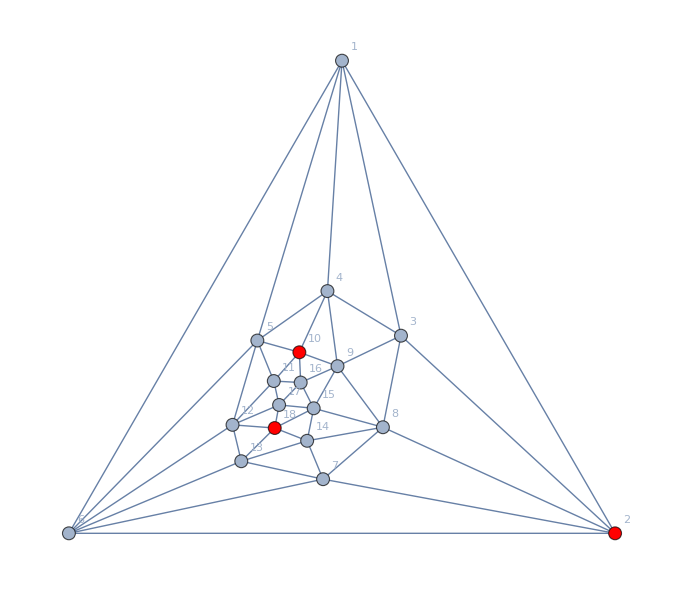

```mathematica
Graph[plantri[[11]],GraphLayout->"TutteEmbedding",VertexLabels->"Name",VertexStyle->{2 -> Red, 10 -> Red,18 -> Red}]
```